```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
l=48;
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,l}];
Tc=Table[Max[Table[If[1/fpiall[[j]][[i]]<=2&&1/fpiall[[j]][[i+1]]>100,i,0],{i,1,Length[fpiall[[j]]]}]],{j,1,l}]
mub=Flatten[Table[i*11,{i,1,l}]]
```

{110,109,109,109,109,109,109,108,108,108,107,107,106,106,105,105,104,103,103,102,101,100,99,98,97,96,95,94,93,91,90,88,87,85,84,82,80,78,76,74,72,70,68,65,63,61,58,56}

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528}

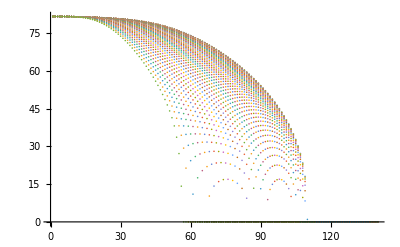

```mathematica
ListPlot[fpiall]
```

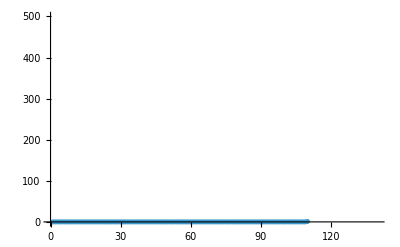

```mathematica
ListPlot[1/fpiall[[1]],PlotRange->{All,{0,500}}]
```

```mathematica
mub2=Flatten[{mub,530}]
```

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,530}

```mathematica
Length[Tc2]
```

51

```mathematica
Tc2=Flatten[{Tc,55.74976}];
```

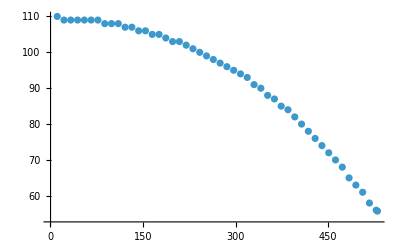

```mathematica
ListPlot[Transpose[{mub2,Tc2}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub2,Tc2}],a+b x^2+c x^4,{a,b,c},x]
```

{a→109.572,b→-0.000154774,c→-1.3961×10^-10}

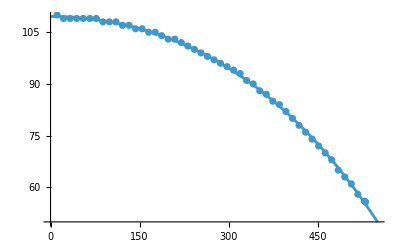

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,550}],ListPlot[Transpose[{mub2,Tc2}]]]
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600,625,650,675,700};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
```

```mathematica
Export["pb.dat",phaseboundary]
```

pb.dat

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,600,650,700};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
Export["pb2.dat",phaseboundary]
```

pb2.dat